```mathematica
ParallelEvaluate[Off[General::munfl,FindFit::cvmit]];
Off[General::munfl,General::stop,LinearSolve::luc,FindFit::cvmit]
SetDirectory[NotebookDirectory[]]
```

/home/kirscher/kette_repo/limit_cycles/manuscript/graphs

```mathematica
hbar=197.327053;
Mm=938.858;
m1=2 Mm;m2=2 Mm;
μ=m1 m2/(m1+m2);
mh2=(2 μ)/(hbar)^2;
Print["ℏ^2/(2  μ) = ",1/mh2]
cijTh=10^-12;
dbg=False;
```

ℏ^2/(2  μ) = 20.7369

Read LEC list (e.g. fitted to two-body scattering length via <<<Fit_Scattering_length.nb>>>)

```mathematica
(* Nuclear E2=2.22 E3=8.48 ℏc=198*)
(* λ a0,r0 (Martin, 23) a1,r1 (Martin,45) a0 (Rimas, unprojected, 6) a1 (Rimas, unprojected, 7) a0 (Rimas, projected, 8) a1 (Rimas, projected, 9)*)
(*LECsNUCL=Import["../LECs_nucl_Rimas-Martin.dat","Table"];
activeLEC=LECsNUCL[[All,{1,2}]][[2;;]];*)
activeLEC=Import["LECS.dat","Table"]
```

{{#,(ecce),the,3-body,LECs,are,renormalized,to,a,constant,B(3,groundstate)=8.48MeV,for,*all*,dimer,binding,energies},{#,L[fm^-1],C_0[b2=0.5],C_0[b2=1.0],C_0[b2=2.22],C_0[b2=5],C_0[b2=7],C_0[b2=10],D_0[b2=0.5],D_0[b2=1.0],D_0[b2=2.22],D_0[b2=5],D_0[b2=7],D_0[b2=10]},{4,-473.112,-484.931,-505.095,-536.711,-554.536,-577.478,668.05,862.333,1388.44,4578.68,23236.7,0.},{6,-701.891,-716.237,-740.666,-778.775,-800.166,-827.603,1305.54,1678.41,2823.86,11401.4,99525.4,0.},{8,-929.686,-946.182,-974.213,-1017.79,-1042.21,-1073.41,2100.03,2764.11,4864.62,26594.4,302419.,0.},{10,-1156.86,-1175.25,-1206.45,-1254.86,-1281.9,-1316.46,2928.63,4149.54,7686.28,50852.,906370.,0.}}

Calculate the dimer wave function in a Gaussian basis rdimer=∑_(i=1)^N c_i·e^(-α_i r^2)

```mathematica
I1=Compile[{lam,b1,b2},(Pi/(2b1+2 b2+4 lam))^(3/2)];
I3=Compile[{b1,b2},3 b1 b2 Pi^(3/2)/(2^(1/2)(b1+b2)^(5/2))];
```

```mathematica
ham=Compile[{lam,b1,b2,lec},Module[{},lec I1[lam,b1,b2]+(1/mh2) I3[b1,b2]]];
norm=Compile[{b1,b2},Module[{},(Pi/(2 b1+2 b2))^(3/2)]];
```

```mathematica
CalcDimerE[basisW_,lam_,lec_]:=
Module[{eval,evec},
Nd=Length[basisW];
hamm=Table[ham[lam,basisW[[i]],basisW[[j]],lec],{i,Nd},{j,Nd}];
normm=Table[norm[basisW[[i]],basisW[[j]]],{i,Nd},{j,Nd}];
{eval,evec}=Eigensystem[{hamm,normm}];
ord=Ordering[Re[eval]];
eigsorted=Re[eval[[ord]]];
vecsorted=evec[[ord]];
{eigsorted[[1]],Transpose[{vecsorted[[1]],basisW}]}
];
```

```mathematica
RiccatiBesselJ=Compile[{z,l},z SphericalBesselJ[l,z]];
RiccatiBesselN=Compile[{z,l},(-1)^l z SphericalBesselY[l,z]];
```

```mathematica
(*Boundery conditions for the wavefunction*)
alpha=Compile[{ra,ka,la,ha},RiccatiBesselN[ka (ra+ha),la]/RiccatiBesselN[ka ra,la]];

beta=Compile[{rb,kb,lb,hb},RiccatiBesselJ[kb (rb+hb),lb]-RiccatiBesselJ[kb rb,lb] (RiccatiBesselN[kb (rb+hb),lb]/RiccatiBesselN[kb rb,lb])];
```

reference: J. Spanier, K.B. Oldham - An Atlas of Functions (1987)

x·j_n(x)=√((π x)/2)J_(n+1/2)(x)=^(x∈C)√((π x)/2)i^(n+1/2) I_(n+1/2)(Re[x])
with
 j_n: spherical Bessel (1st kind)
 J_n: Bessel (1st kind)
 I_n: modified Bessel (1st kind)
 to optimize runtime, we substitute in this implementation -- valid for S-wave scattering, only:
 j_0(i x)=Sinh[x]/x
 and
 j_1(i x)=i x^-1(Cosh[x]-Sinh[x]/x)
 For numerical stability at arguments x>>1, it is curucial to subsitute the following representation:
 e^(-aR^2-bR'^2) Sinh[bRR']=1/2(e^(-aR^2-bR'^2+bRR')-e^(-aR^2-bR'^2-bRR')) and similarly for the hyperbolic cosine;
 Retaining the Sinh built-in function throws, at best, warnings, and yields significantly inaccurate and almost certainly non-sensical results!

```mathematica
NormTF=Compile[{{core,_Real,2}},Total[Flatten[Table[core[[i]][[1]] core[[j]][[1]] core[[k]][[1]] core[[l]][[1]] (1/2^(7/2)) (Pi/((core[[i]][[2]]+core[[j]][[2]]) (core[[k]][[2]]+core[[l]][[2]])))^(3/2),{i,Length[core]},{j,Length[core]},{k,Length[core]},{l,Length[core]}]]]];


VlocTF=Compile[{r,lam,Cc,Dd,Aa,Bb,Gg,Hh},Block[{eta2,eta3,w2,w3},
eta2=(π^(3/2)/4) Cc/(lam Bb + Aa(lam + 2Gg +2  Bb) + lam Hh +2 Bb Hh+Gg(lam +2Hh))^(3/2);
w2= 2lam(Aa+Hh)(Gg+Bb)/(lam Bb + Aa(lam+2 Gg+2Bb)+lam Hh +2 Bb Hh+Gg(lam+2Hh));
eta3 =(π^(3/2)/4) Cc/(lam Bb + Gg(lam + 2Bb)+lam Hh +2Bb Hh + Aa(lam+2Gg+2Hh))^(3/2);
w3 = 2lam(Aa+Bb)(Gg+Hh)/(lam Bb + Gg(lam+2Bb)+lam Hh +2Bb Hh+Aa(lam+2Gg+2Hh));
eta2 Exp[-w2 r^2]+eta3 Exp[-w3 r^2]
]];

WnolocTF3=Compile[{r,rp,Ee,lam,Cc,Dd,Aa,Bb,Gg,Hh,Ll,TwoMyOverHBsq},Block[{zeta1,zeta2,zeta3,a1,b1,c1,a2,b2,c2,a3,b3,c3,Sinh1,Sinh2,Sinh3,CoshA},
zeta1=-(π^(3/2)/(√2))/(Aa+Bb+Gg+ Hh)^(3/2) (1/TwoMyOverHBsq);
a1=(4Bb Hh + Gg Bb+Gg Hh+Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
b1=(2Gg Bb -2Gg Hh -2 Aa Bb +2 Aa Hh)/(2Aa+2Bb+2Gg+2Hh);
c1=(Gg Bb +Hh Gg+4Aa Gg +Aa Bb +Aa Hh)/(2Aa+2Bb+2Gg+2Hh);

zeta2=-(π^(3/2)/(√2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);
zeta3=-(π^(3/2)/(√2)) Cc/(2lam+Aa +Bb+ Gg+Hh)^(3/2);

a2=(4Hh(2lam+Bb)+Gg(2lam +Bb+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b2=(Gg(4 lam+2 Bb-2 Hh)+Aa (-4 lam-2 Bb+2 Hh))/(2 (2 lam+Aa+Bb+Gg+Hh));
c2=( Gg(2lam+Bb+Hh)+Aa(2lam+4Gg+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

a3= (4Bb(2lam+Hh)+Gg(Bb+2lam+Hh)+Aa(2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));
b3=(Gg(2Bb-4lam-2Hh)+Aa(4lam+2Hh-2Bb))/(2(2 lam+Aa+Bb+Gg+Hh));
c3=(Gg(Bb+2lam+Hh)+Aa(4Gg+2lam+Bb+Hh))/(2(2 lam+Aa+Bb+Gg+Hh));

(* these conditions avoid having to multiply a Gaussian whose argument is larger than that of a Sinc with the
latter which amounts only to a numerical zero; if we assume any number <= 10^-14 to be zero, numRAD ≈ 217 *)

Sinh1=If[b1==0,0,(Exp[b1 r rp-a1 r^2-c1 rp^2]-Exp[-b1 r rp-a1 r^2-c1 rp^2])/(2 b1)];
Sinh2=If[b2==0,0,(Exp[b2 r rp-a2 r^2-c2 rp^2]-Exp[-b2 r rp-a2 r^2-c2 rp^2])/(2 b2)];
Sinh3=If[b3==0,0,(Exp[b3 r rp-a3 r^2-c3 rp^2]-Exp[-b3 r rp-a3 r^2-c3 rp^2])/(2 b3)];

-(4 Pi) (zeta1 ((-(4 a1^2 r^2+b1^2 rp^2-2 a1)- TwoMyOverHBsq Ee) Sinh1-4 a1 Sqrt[3]^-1 (-0.5 r rp (Exp[b1 r rp-a1 r^2-c1 rp^2]+Exp[-b1 r rp-a1 r^2-c1 rp^2])+Sinh1))+zeta2 Sinh2+zeta3 Sinh3)
]];
```

```mathematica
SolveSecularP3[Rdis_?NumberQ,Npoints_?NumberQ,momentum_?NumberQ,Lin_?NumberQ,lam_?NumberQ,c0_?NumberQ,d0_?NumberQ,a00_?ArrayQ,TwoMyOverHBsq_?NumberQ]:=Block[{hDif,Dmat,Kmat,Wmat,bcol,Amat,ucol,wf,tanDelta,usol,energyMeV,nff,cij},
t1=AbsoluteTime[];
hDif=Rdis/Npoints;
energyMeV=(momentum^2)/TwoMyOverHBsq;
Kmat=SparseArray[{Band[{1,1}]->-2,Band[{2,1}]->1,Band[{1,2}]->1},{Npoints,Npoints}];

normsqu=1/NormTF[a00];

(*Wmat=ConstantArray[0,{Npoints,Npoints}];*)

Wmats={};
SetSharedVariable[Wmats];

ParallelDo[

cij=a00[[ii]][[1]] a00[[jj]][[1]] a00[[kk]][[1]]  a00[[ll]][[1]]  normsqu;

amat=DiagonalMatrix[Table[-hDif^2 TwoMyOverHBsq VlocTF[i hDif,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]]],{i,1,Npoints}]];

wmat=Table[-hDif^3 TwoMyOverHBsq WnolocTF3[i hDif,j hDif,energyMeV,lam,c0,d0,a00[[ii]][[2]],a00[[jj]][[2]],a00[[kk]][[2]],a00[[ll]][[2]],Lin,TwoMyOverHBsq],{i,1,Npoints},{j,1,Npoints}(*,ProgressReporting->False*)]; 

AppendTo[Wmats,cij (amat+wmat)];
(*AppendTo[Wmats,cij amat];*)

,{ii,1,Length[a00]},{jj,1,Length[a00]},{kk,1,Length[a00]},{ll,1,Length[a00]}];

Wmat=Total[Wmats];
Dmat=DiagonalMatrix[Table[hDif^2 (momentum^2-(Lin (Lin+1))/(i hDif)^2),{i,1,Npoints}]];

Amat=Kmat+Dmat+Wmat;

bcol=ConstantArray[0,Npoints];
ucol=Array[Subscript["u", ##]&,{Npoints}];

bcol⟦-1⟧=- beta[Rdis,momentum,Lin,hDif];
Amat⟦-1⟧⟦-1⟧=Amat⟦-1⟧⟦-1⟧+alpha[Rdis,momentum,Lin,hDif];

usol=LinearSolve[Amat,bcol];
relerr=Norm[Amat.usol-bcol]/Norm[usol];
Print["relative error in wave-function solution = ",relerr];

(*tanDelta= (RiccatiBesselJ[momentum Rdis,Lin]/RiccatiBesselN[momentum Rdis,Lin])-(usol⟦-1⟧/RiccatiBesselN[momentum Rdis,Lin]);*)
sol=NSolve[usol⟦-1⟧==RiccatiBesselJ[momentum Rdis,Lin]-RiccatiBesselN[momentum Rdis,Lin] xx,xx,Reals];
tanDelta=xx/.sol[[-1]];
t2=AbsoluteTime[];
Print["finite-difference runtime Δt = ",(t2-t1)/60.," mins     p_match·r_max = ",momentum Rdis];
{tanDelta,usol}
];
```

```mathematica
GetEREP3[l_,rMax_,nPoints_,core_,LECc_,energ_:0.001]:=Module[{locall=l},
LECd=0.0;
momFM=Sqrt[mh2 energ];
{TanDelSwave,wfkt}=SolveSecularP3[rMax,nPoints,momFM,0,locall,LECc,LECd,core,mh2];
{-TanDelSwave/Sqrt[mh2 energ ],wfkt}
]
```

alternative to the stochastic and inefficient search for an appropriate basis, one can invoke a genetic optimization (external Python/Fortran program, look for <bridgeA2_tmp.py> and calls therein)
and feed the results to the function <CalcDimerE[]> (see above

{{0.,1.},{0.1,0.114563},{0.2,0.0131247},{0.3,0.0015036},{0.4,0.000172257},{0.5,0.0000197342},{0.6,2.26081×10^-6},{0.7,2.59005×10^-7},{0.8,2.96724×10^-8},{0.9,3.39936×10^-9},{1.,3.8944×10^-10},{1.1,4.46154×10^-11},{1.2,5.11127×10^-12},{1.3,5.85563×10^-13},{1.4,6.70838×10^-14},{1.5,7.68531×10^-15},{1.6,8.80452×10^-16},{1.7,1.00867×10^-16},{1.8,1.15556×10^-17},{1.9,1.32385×10^-18},{2.,1.51664×10^-19}}

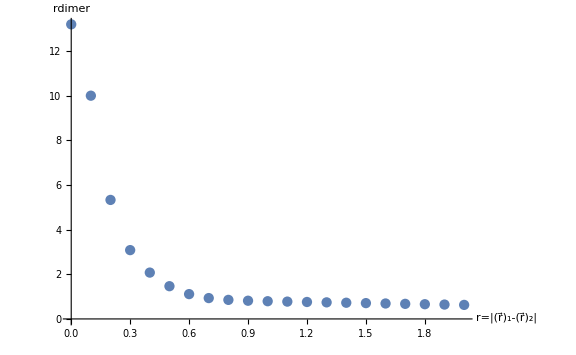

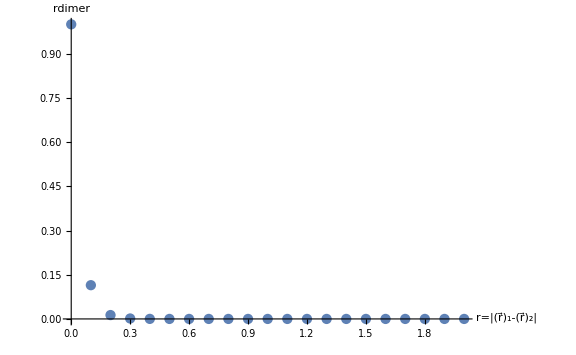

```mathematica
lambdaTest=10;
bd={0.5,1,3,5,7,10};
bdtest=2;
LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[bdtest]];

(*one dimer to rule them all*)
dCores={{0.43,{{8.295038245760063,43.077078050043276},{4.019686413680822,7.547281233430226},{0.2282575086167419,0.36945978744917085},{0.6542323470635848,0.031554706184736526}}}};

JacobiTrailWavefunctionU=Total[Abs[#[[1]]] Exp[-#[[2]] r1^2]&/@#[[2]]]&/@dCores;rR=Range[0,2,0.100];
JacobiTrailWavefunctionDataU=Table[#/.{r1->R1},{R1,rR}]&/@JacobiTrailWavefunctionU;

plotData=Transpose[{rR,#}]&/@JacobiTrailWavefunctionDataU;
plotDataExp=Table[{rr,Exp[-√(Mm bd[[bdtest-1]]) rr]},{rr,rR}]
lgd="";

ListPlot[plotData,PlotRange->Full,AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large,PlotLabels->Automatic]
ListPlot[plotDataExp,PlotRange->Full,AxesLabel->{"r=|(r⃗)_1-(r⃗)_2|","TemplateBox[{\"r\", \"dimer\"},\"BraKet\"]"},PlotLegends->lgd,ImageSize->Large,PlotLabels->Automatic]
```

```mathematica
(* energy at which the scattering length is obtained from the amplitude *)
energ=0.1;
(* Integration grid *)
rMa=8;
grdPerFermi=10;
nGrd=IntegerPart[rMa grdPerFermi];
results={};
(*dCores=Get["dimerCores_"<>ToString[lambdaTest]<>".dat"];*)
nbrOfCores=Length[dCores];

Do[
(*{e0Core,dimerCore}=dCores[[nn]];*)
{e0Core,dimerCore}=dCores[[nn]];

dimCore=Length[dimerCore];

tmp=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ][[1]];
AppendTo[results,{lambdaTest,LECc,rMa,nGrd,e0Core,dimCore,tmp,tmp/(hbar/√(Mm Abs[e0Core]))}];
Print["core ",nn," )  λ=",lambdaTest," ; C_0(λ)=",LECc," ; R_max=",rMa," ; #=",nGrd," ; E_match=",energ," ; B(2)=",e0Core," ; dim_d=",dimCore," ; a_dd=",tmp," ; a_dd/a_aa=",tmp/(hbar/√(Mm Abs[e0Core]))];
,{nn,{1}}];
```

relative error in wave-function solution = 4.48569×10^-16

finite-difference runtime Δt = 0.0345319 mins     p_match·r_max = 0.555544

core 1 )  λ=10 ; C_0(λ)=-1156.86 ; R_max=8 ; #=80 ; E_match=0.1 ; B(2)=0.43 ; dim_d=4 ; a_dd=6.99317 ; a_dd/a_aa=0.712069

### maximal-integration-range dependence of the a_dd scattering-length pre/post-diction

relative error in wave-function solution = 3.77956×10^-16

finite-difference runtime Δt = 0.113801 mins     p_match·r_max = 1.87496

core 1 )  λ = 10   C_0(λ) = -1156.86     R_max = 27.     #(grid points) = 162                a_dd = 8.92764 fm        a_dd/a_aa = 0.909043

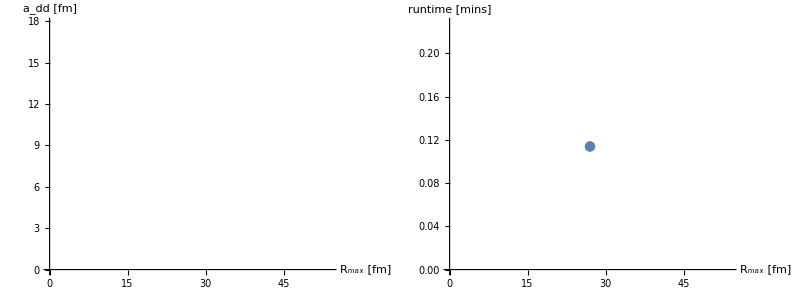

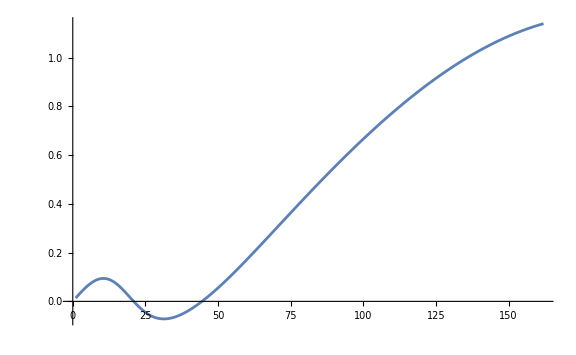

```mathematica
grdPerFermi=6;
rMaxStart=27;
rMaxEnd=27;
nbrR=1;
coreNBR=1;
{e0Core,dimerCore}=dCores[[coreNBR]];
RmaxRange=Range[rMaxStart,rMaxEnd,N[(rMaxEnd-rMaxStart)/nbrR]];

results={};
resultsWF={};
runtimes={};

(*SetSharedVariable[results,resultsPhases];*)
Do[
nGrd=IntegerPart[rMa grdPerFermi];
ta=AbsoluteTime[];
{tmp,tmp2}=GetEREP3[lambdaTest,rMa,nGrd,dimerCore,LECc,energ];
tb=AbsoluteTime[];
AppendTo[results,tmp];
AppendTo[resultsWF,tmp2];
AppendTo[runtimes,{rMa,(tb-ta)/60.}];
Print["core ",coreNBR," )  λ = ",lambdaTest,"   C_0(λ) = ",LECc,"     R_max = ",rMa,"     #(grid points) = ",nGrd,"                a_dd = ",tmp," fm        a_dd/a_aa = ",Style[tmp/(hbar/√(Mm Abs[e0Core])),Red,18]];
,{rMa,RmaxRange}]

Grid[{{ListPlot[Transpose[{RmaxRange,results}],ImageSize->Large,Joined->True,AxesLabel->{"R_max [fm]","a_dd [fm]"}],ListPlot[runtimes,ImageSize->Large,AxesLabel->{"R_max [fm]","runtime [mins]"}]}}]
ListPlot[resultsWF,Joined->True,PlotRange->Full,ImageSize->Large]
```

{{nm→1.00711,tandd→-0.604054}}

CompiledFunction::cfex: Could not complete external evaluation at instruction 2; proceeding with uncompiled evaluation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

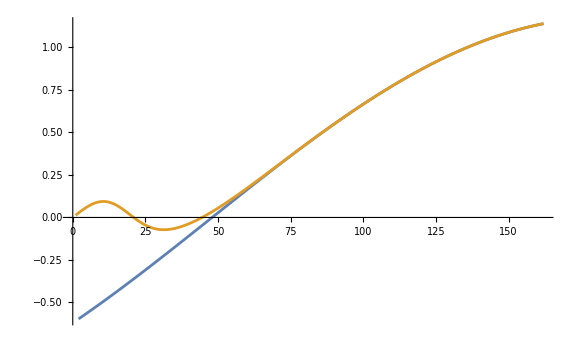

a_dd = 8.69856     a_dd/a_aa = 0.885716

```mathematica
momFM=Sqrt[mh2 energ];
rRan=Range[0,rMaxEnd,1/grdPerFermi];
match1=1;
match2=5;

sol=NSolve[{resultsWF[[-1]][[-match1]]==nm (RiccatiBesselJ[momFM (rMaxEnd-match1/grdPerFermi),0]-tandd RiccatiBesselN[momFM (rMaxEnd-match1/grdPerFermi),0]),
resultsWF[[-1]][[-match2]]==nm (RiccatiBesselJ[momFM (rMaxEnd-match2/grdPerFermi),0]-tandd RiccatiBesselN[momFM (rMaxEnd-match2/grdPerFermi),0])},{nm,tandd},Reals]

RiccatiBJN=Table[(nm (RiccatiBesselJ[momFM r,0]-tandd RiccatiBesselN[momFM r,0])),{r,rRan}];
RiccatiBJN=RiccatiBJN/.sol[[1]];
ListPlot[{RiccatiBJN[[;;-2]],resultsWF[[-1]]},Joined->True,PlotRange->Full,ImageSize->Large]
add=(-tandd/.sol[[1]][[2]])/Sqrt[mh2 energ ];
Print["a_dd = ",add, "     a_dd/a_aa = ",add/(hbar/√(Mm Abs[e0Core])) ]
```

λ = 8 fm^-2  non-local

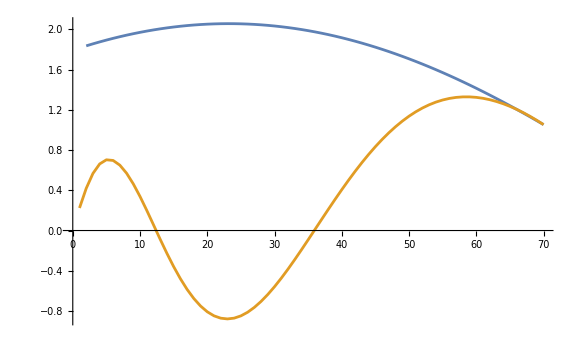

a_dd = -8.50457     a_dd/a_aa = -1.29223

λ = 8 fm^-2  local

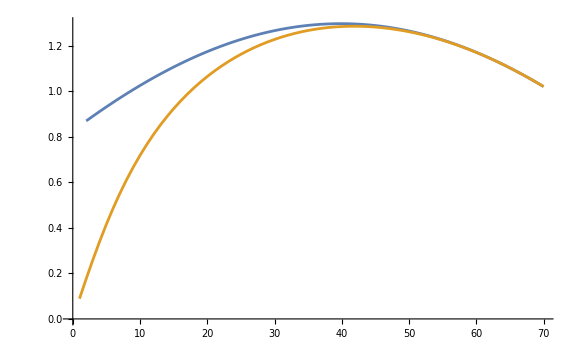

a_dd = -3.91756     a_dd/a_aa = -0.595254

EFT parameters | Numerical parameters | plot control
cutoff regulator λ = 10 | R_max = 17 | #(plot grid points) = 40
C_0(λ) = -1156.86 | #(Integration grid points) = 51 | plot threshold =  0.001
B(2) = 0.43 | dimer-basis dimension = 4 |

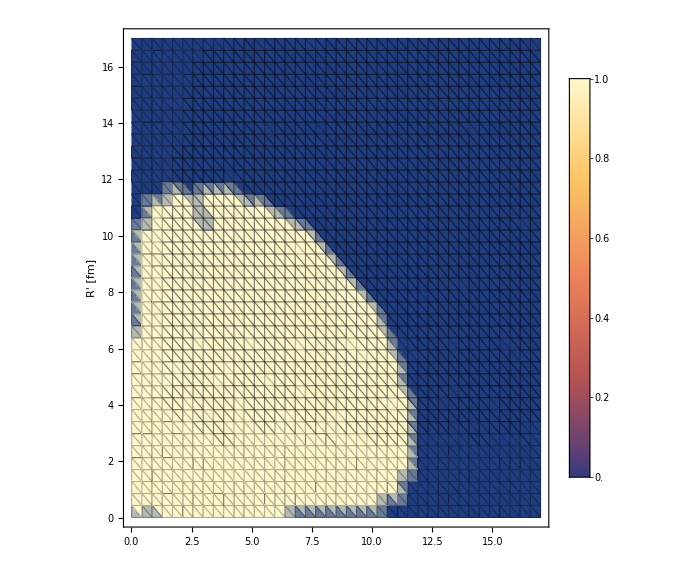
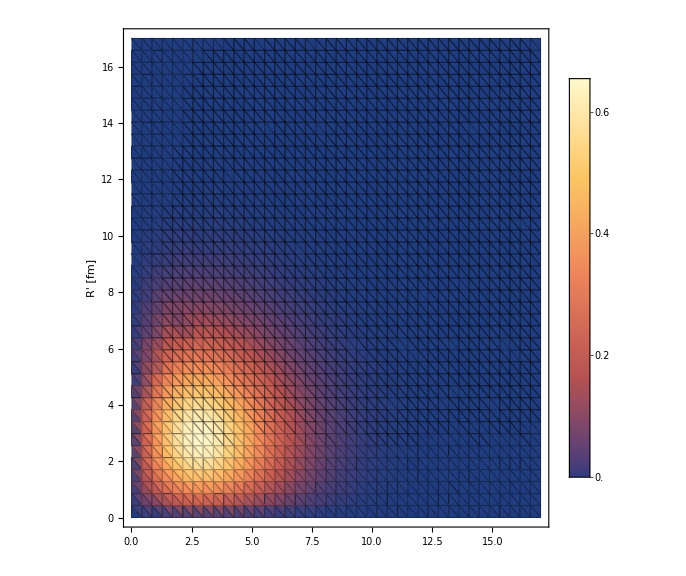
-Graphics- | -Graphics-

```mathematica
(* Integration grid *)
rMa=rMaxEnd;
grdPerFermi=3;
nGrd=IntegerPart[rMa grdPerFermi];

(* Plot parameters for the visualization of V(r,r') *)
nR=40;rMi=0.01;thresh=10^-3;

normCore=1/NormTF[dimerCore];
dimCore=Length[dimerCore];

LECc=Flatten[Select[activeLEC,#[[1]]==lambdaTest&]][[2]];
Grid[{{"EFT parameters","Numerical parameters","plot control"},{"cutoff regulator λ = "<>ToString[lambdaTest],"R_max = "<>ToString[rMa],"#(plot grid points) = "<>ToString[nR]},{"C_0(λ) = "<>ToString[LECc],"#(Integration grid points) = "<>ToString[nGrd],"plot threshold = "NumberForm[N[thresh]]},{"B(2) = "<>ToString[e0Core],"dimer-basis dimension = "<>ToString[dimCore]}},Frame->All]

rR=Range[rMi,rMa,(rMa-rMi)/nR];
nR=Length[rR];

potnoloc3d={};
Do[
cij=dimerCore[[ii]][[1]] dimerCore[[jj]][[1]] dimerCore[[kk]][[1]]  dimerCore[[ll]][[1]]  normCore;
potnoloc3dtmp=
Flatten[ParallelTable[{rR[[i]],rR[[j]],mh2 cij WnolocTF3[rR[[i]],rR[[j]],energ,lambdaTest,LECc,0.0,dimerCore[[ii]][[2]],dimerCore[[jj]][[2]],dimerCore[[kk]][[2]],dimerCore[[ll]][[2]],0,mh2]}
,{i,Length[rR]},{j,Length[rR]}],1];
AppendTo[potnoloc3d,potnoloc3dtmp]
,{ii,1,dimCore},{jj,1,dimCore},{kk,1,dimCore},{ll,1,dimCore}]
potnonloc3d=Transpose[{potnoloc3d[[1]][[All,1]],potnoloc3d[[1]][[All,2]],Total[potnoloc3d[[All,All,3]]]}];
chopedMat=ParallelTable[
If[Abs[Re[potnonloc3d[[i]][[3]]]]>=thresh,{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],1},{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],0}]
,{i,Length[potnonloc3d]}];
Grid[{{
ListDensityPlot[chopedMat,Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
,
ListDensityPlot[Re[potnonloc3d],Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
}}]
Put[potnonloc3d,"nonlocPot_"<>ToString[lambdaTest]<>".dat"];
```

w/o  small  widthpara

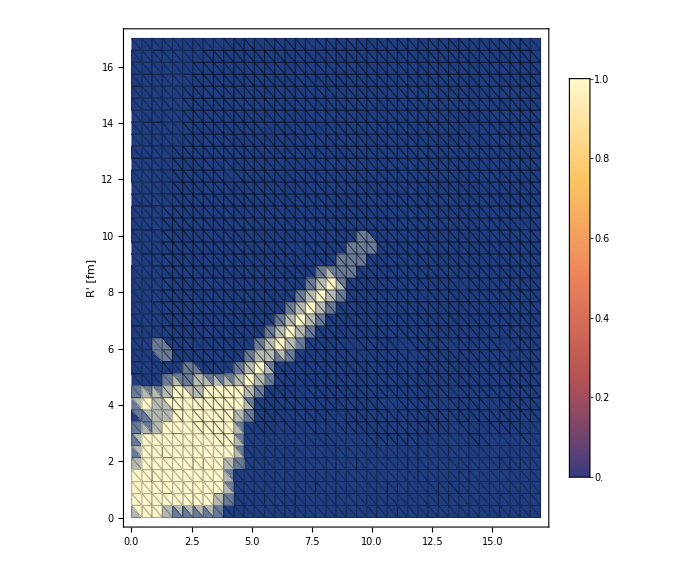
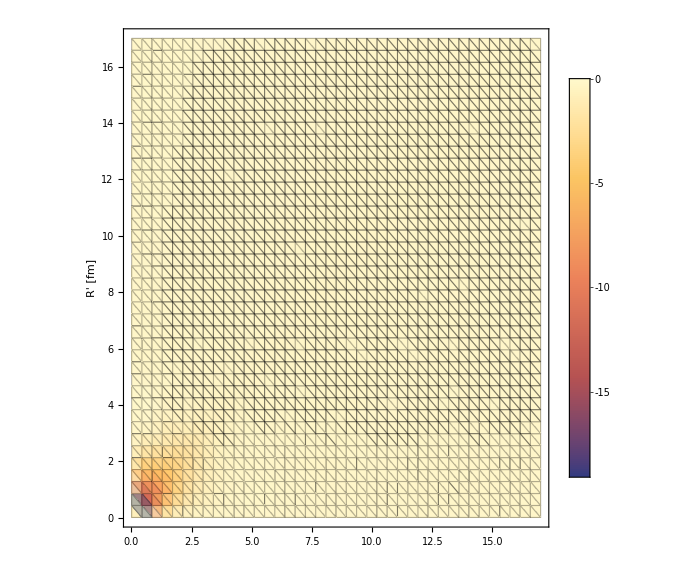
-Graphics- | -Graphics-

```mathematica
potnonloc3d=Transpose[{potnoloc3d[[1]][[All,1]],potnoloc3d[[1]][[All,2]],Total[potnoloc3d[[All,All,3]]]}];
chopedMat=ParallelTable[
If[Abs[Re[potnonloc3d[[i]][[3]]]]>=0.1,{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],1},{potnonloc3d[[i]][[1]],potnonloc3d[[i]][[2]],0}]
,{i,Length[potnonloc3d]}];
Grid[{{
ListDensityPlot[chopedMat,Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
,
ListDensityPlot[Re[potnonloc3d],Mesh->All,PlotRange->All,PlotLegends->Automatic,ImageSize->Large,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"R' [fm]",None},{None,"R [fm]"}},FrameTicks->All]
}}]
Put[potnonloc3d,"nonlocPot_"<>ToString[lambdaTest]<>".dat"];
```